```mathematica
SetDirectory[NotebookDirectory[]]
```

/data2/users/sanderson/Research/KLStats/Isochrone/WithGaiaErrors

Conversion factor between km/s and kpc/Myr to a zillion (16) sigfigs

```mathematica
kmsTokpcMyr=0.001022729843472133;
```

Define the “true” potential

```mathematica
Phi[r_,M_,b_]:=-M/(b+Sqrt[b^2+r^2])
PhiEff[r_,L_,M_,b_]:=-M/(b+Sqrt[b^2+r^2])+L^2/(2 r^2)
vcirc[r_,M_,b_]:=Sqrt[(M r^2)/(Sqrt[b^2+r^2] (b+Sqrt[b^2+r^2])^2)]
```

```mathematica
Jr[r_,pr_,L_,M_,b_]:=M/Sqrt[-pr^2-L^2/r^2+2 M/(b+Sqrt[b^2+r^2])]-1/2 (L+Sqrt[L^2+4 M b]/2)
```

Pick initial (x,v) of satellite centers of mass and convert to (J_r^0, L^0, L_z^0) and initial thetas

This ensures that at least a bit of the stream will pass close enough to the Sun to get in Gaia’s range

```mathematica
x0={{8.5,0,0}};   (*in kpc*)
v0={{170,50,300}};   (*in km/s*)
```

```mathematica
posInName="pos.COM.dat"
velInName="vel.COM.dat"
JOutName="J.COM.dat"
thetaOutName="theta.COM.dat"
```

```mathematica
pStream=OpenRead[posInName]
vStream=OpenRead[velInName]
Write[pStream,Length[x0]];
Export[pStream,x0,"Data"];
Export[vStream,v0,"Data"];
Close[pStream]
Close[vStream]
```

## run cartToAA manually on initial positions

```mathematica
Dimensions[JCOM=ReadList[JOutName,{Number,Number,Number}]]
Dimensions[thetaCOM=ReadList[thetaOutName,{Number,Number,Number}]]
```

```mathematica
JCOM
thetaCOM
```

Construct streams as clumps in (Jr, L, L_z) space

Note that we need all three numbers to describe the collection of orbits so that we know the relative inclinations - we can assume phase-mixing though so the distribution in Θ is just uniform from 0 to 2π for these things

```mathematica
Ns=1;
sigmas={0.005}(*,0.02,0.05,0.07}*)(*RandomReal[{0,.1},Ns]*)
```

{0.005}

We have to sample the angular momentum as a (magnitude, angle) pair, since L and Lz are not strictly independent of one another (you can’t have Lz>L). So this table constructs distributions that are Gaussian in cosi, L and Jr, and then we convert to Lz after the distribution is sampled.

```mathematica
spikyDist=MixtureDistribution[RandomReal[{0.1,1},Ns],Table[MultinormalDistribution[{RandomReal[{-1,1}],RandomReal[{2,10}],RandomReal[{0,10}]},DiagonalMatrix[{sigmas[[i]]/10,sigmas[[i]],sigmas[[i]]}]],{i,1,Ns}]]
```

MultinormalDistribution[{-0.70215,2.88154,8.43185},{{0.0005,0.,0.},{0.,0.005,0.},{0.,0.,0.005}}]

```mathematica
Nstars=50000;
```

```mathematica
Dimensions[trueJrL=RandomVariate[spikyDist,Nstars]]
```

{50000,3}

Throw out anything outside the cos i range [-1,1] or with negative Jr and resample:

```mathematica
For[i=1,i≤Nstars,i++, While[(Abs[trueJrL[[i,1]]]>1)||(trueJrL[[i,3]]<0),trueJrL[[i]]=RandomVariate[spikyDist]]]
```

```mathematica
Select[trueJrL[[All,1]],#<-1&]
```

{}

```mathematica
Select[trueJrL[[All,3]],#<0&]
```

{}

```mathematica
Dimensions[trueActions=Transpose[{trueJrL[[All,1]]*trueJrL[[All,2]],trueJrL[[All,2]],trueJrL[[All,3]]}]]
```

{50000,3}

The random realization shows us that the points fall in clumps in action space:

```mathematica
ListPointPlot3D[trueActions,PlotRange->{{-12,12},{-12,12},{0,12}},AspectRatio->1]
```

-Graphics3D-

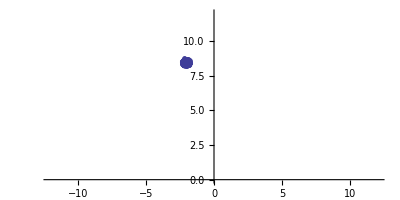

```mathematica
ListPlot[trueActions[[All,{1,3}]],PlotRange->{{-12,12},{0,12}},AspectRatio->1/2]
```

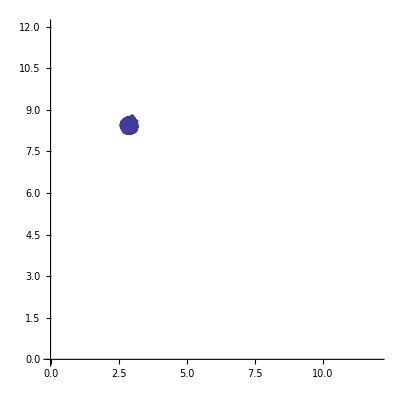

```mathematica
ListPlot[trueActions[[All,{2,3}]],PlotRange->{{0,12},{0,12}},AspectRatio->1]
```

We also need the angles, which are phase-mixed:

```mathematica
Dimensions[trueAngles=Transpose[{RandomReal[{0,2π},Nstars],RandomReal[{0,2π},Nstars],RandomReal[{0,2π},Nstars]}]]
```

{50000,3}

```mathematica
Dimensions[initAngles=Transpose[{RandomVariate[NormalDistribution[1.0,2π/1000],Nstars],RandomVariate[NormalDistribution[2.0,2π/1000],Nstars],RandomVariate[NormalDistribution[6.0,2π/1000],Nstars]}]]
```

{50000,3}

```mathematica
(*initAngles=Table[{0,0,0},{i,1,Nstars}];*)
```

Convert coordinates to configuration space (x,v)

This is done using a C program called through MathLink

```mathematica
link=Install["../AAToCart/aa_to_cart_math"]
```

LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math,9,8]

```mathematica
trueCart=Table[{0,0,0,0,0,0},{i,1,Nstars}];
```

```mathematica
For[i=1, i≤Nstars, i++,trueCart[[i]]=AAToCart[trueActions[[i]],trueAngles[[i]]]]
```

```mathematica
initCart=Table[{0,0,0,0,0,0},{i,1,Nstars}];
```

```mathematica
For[i=1, i≤Nstars, i++,initCart[[i]]=AAToCart[trueActions[[i]],initAngles[[i]]]]
```

```mathematica
Uninstall[link]
```

/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math

### plots of the cartesian distribution

```mathematica
ListPointPlot3D[trueCart[[All,1;;3]],PlotRange->{{-80,80},{-80,80},{-80,80}},AspectRatio->1]
```

-Graphics3D-

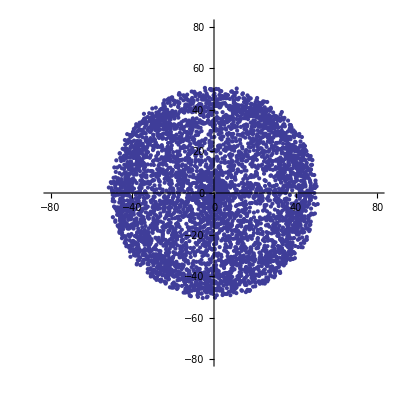

```mathematica
ListPlot[trueCart[[All,1;;2]],PlotRange->{{-80,80},{-80,80}},AspectRatio->1]
```

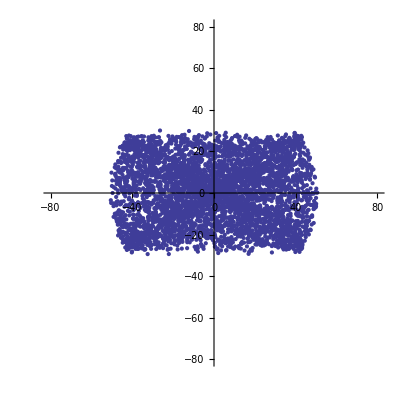

```mathematica
ListPlot[trueCart[[All,2;;3]],PlotRange->{{-80,80},{-80,80}},AspectRatio->1]
```

```mathematica
ListPointPlot3D[initCart[[All,1;;3]],PlotRange->All(*PlotRange->{{-50,50},{-50,50},{-5,5}},AspectRatio->1*)]
```

-Graphics3D-

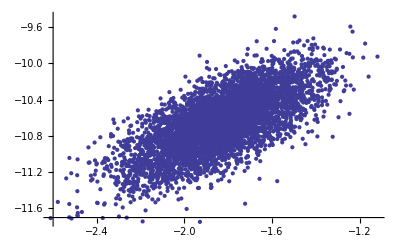

```mathematica
ListPlot[initCart[[All,1;;2]],PlotRange->All(*{{-60,40},{-50,50}},AspectRatio->1*)]
```

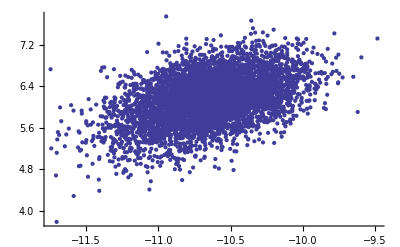

```mathematica
ListPlot[initCart[[All,2;;3]],PlotRange->All(*{{-60,-40},{15,35}},AspectRatio->1*)]
```

```mathematica
{x0,y0,z0,vx0,vy0,vz0}=Mean[initCart]
```

{-1.83263,-10.6497,6.14976,0.0542006,-0.725726,0.359278}

```mathematica
{dx,dy,dz,dvx,dvy,dvz}={initCart[[All,1]]-x0,initCart[[All,2]]-y0,initCart[[All,3]]-z0,initCart[[All,4]]-vx0,initCart[[All,5]]-vy0,initCart[[All,6]]-vz0};
```

```mathematica
Mean[Sqrt[dx^2+dy^2+dz^2]]
```

0.531404

```mathematica
Mean[Sqrt[dvx^2+dvy^2+dvz^2]]*978
```

26.1383

```mathematica
Sqrt[(x0+8.0)^2+y0^2+z0^2]
```

13.7576

```mathematica
ListPointPlot3D[978*trueCart[[All,4;;6]],PlotRange->{{-1000,1000},{-1000,1000},{-1000,1000}},AspectRatio->1]
```

-Graphics3D-

```mathematica
Position[trueCart[[All,1]],Indeterminate]
```

{}

### Split up coordinates into positions and velocities

```mathematica
initPositions=initCart[[All,1;;3]];
initVelocities=initCart[[All,4;;6]]/kmsTokpcMyr;
```

```mathematica
truePositions=trueCart[[All,1;;3]];
trueVelocities=trueCart[[All,4;;6]]/kmsTokpcMyr;
```

```mathematica
trueDists=Sqrt[(truePositions[[All,1]]-8)^2+truePositions[[All,2]]^2+truePositions[[All,3]]^2];
```

### Histogram of distances from the Sun to the stream stars

```mathematica
dbins=Table[id,{id,0,80,1}];
dcounts=BinCounts[trueDists,{dbins}];
```

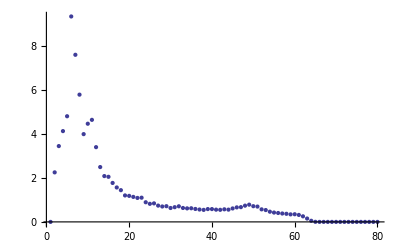

```mathematica
ListPlot[Transpose[{dbins[[2;;Length[dbins]]],dcounts/(dbins[[2;;Length[dbins]]]^2)}],PlotRange->All]
```

Convert (x,v) to observables, convolve with errors, and convert back to (x’,v’)

NOTE: make sure that these four filenames are the same in here and in data_realization_gaia.f!!!!

```mathematica
fnamePosIn="pos.test.dat"
fnamePosOut="newpos.test.dat"
fnameVelIn="vel.test.dat"
fnameVelOut="newvel.test.dat"
fnameObsOut="obs.dat"
```

pos.test.dat

newpos.test.dat

vel.test.dat

newvel.test.dat

obs.dat

```mathematica
pStream=OpenWrite[fnamePosIn,BinaryFormat->False]
vStream=OpenWrite[fnameVelIn,BinaryFormat->False]
```

OutputStream[pos.test.dat,94]

OutputStream[vel.test.dat,95]

```mathematica
Write[pStream,Length[truePositions]];
Export[pStream,truePositions,"Data"];
Export[vStream,trueVelocities,"Data"];
```

```mathematica
Close[pStream]
Close[vStream]
```

pos.test.dat

vel.test.dat

## At this point, manually run data_realizations_gaia

```mathematica
pStream=OpenRead[fnamePosOut];
vStream=OpenRead[fnameVelOut];
oStream=OpenRead[fnameObsOut];
n1=Read[pStream,Number]
n2=Read[oStream,Number]
Dimensions[convPositions=ReadList[pStream,{Number,Number,Number}]]
Dimensions[convVelocities=ReadList[vStream,{Number,Number,Number}]]
Dimensions[convObs=ReadList[oStream,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}]]
Close[pStream];
Close[vStream];
Close[oStream];
```

50000

50000

{50000,3}

{50000,3}

{50000,11}

columns of observational file are vmag, alpha, delta, parallax, par error, mu_alpha, pm error, mu_delta, pm error, RV, RV error

Data quality cuts (on observational data)

### Histogram of magnitudes - cut out V>20

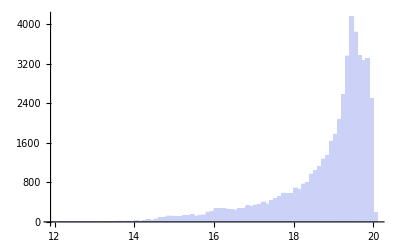

```mathematica
Histogram[convObs[[All,1]]]
```

```mathematica
Tally[magSel=Thread[convObs[[All,1]]<20]]
```

{{True,49810},{False,190}}

### Cut out negative parallaxes, and those with huge errors

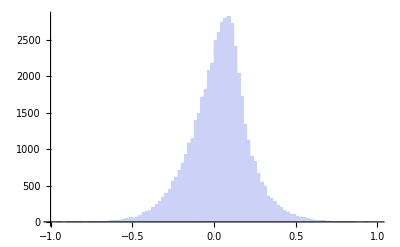

```mathematica
Histogram[convObs[[All,4]],{-1,1,.02}]
```

```mathematica
Tally[posParSel=Thread[(convObs[[All,4]]>0)]]
```

{{True,30612},{False,19388}}

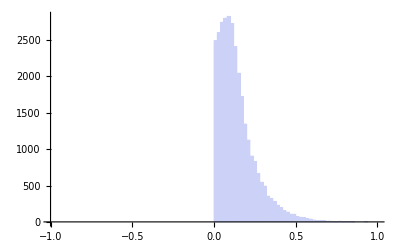

```mathematica
Histogram[Pick[convObs[[All,4]],posParSel],{-1,1,.02}]
```

```mathematica
Tally[hugeParErrSel=Thread[Abs[convObs[[All,5]]]< 1000]]
```

{{True,49810},{False,190}}

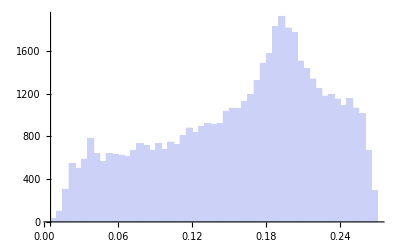

```mathematica
Histogram[Pick[convObs[[All,5]],hugeParErrSel],PlotRange->All]
```

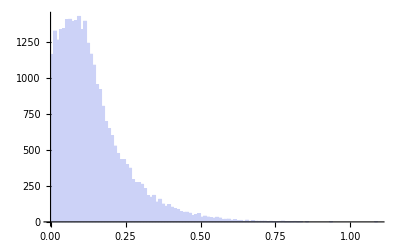

```mathematica
Histogram[Pick[convObs[[All,4]],Thread[posParSel&&hugeParErrSel]],PlotRange->All]
```

### Dataquality cut on parallaxes

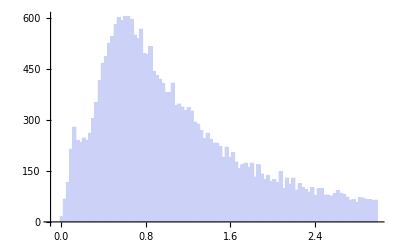

```mathematica
Histogram[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[posParSel&&hugeParErrSel]],{-.1,3,.03}]
```

```mathematica
Tally[dqParSel=Thread[Abs[convObs[[All,5]]/convObs[[All,4]]]<0.3]]
```

{{False,47992},{True,2008}}

### Dataquality cut on proper motions is basically the same as for pars - errors are proportional

### Dataquality cut on RVs

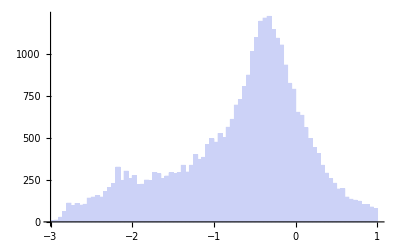

```mathematica
Histogram[Log10[convObs[[All,11]]/convObs[[All,10]]],{-3,1,.05}]
```

```mathematica
Tally[dqRVSel=Thread[Abs[convObs[[All,11]]/convObs[[All,10]]]<0.3]]
```

{{False,29958},{True,20042}}

### Combining all the cuts together

```mathematica
Tally[allSels=Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel&&dqRVSel]]
```

{{False,48041},{True,1959}}

```mathematica
Dimensions[tpSel=Pick[truePositions,allSels]]
```

{1959,3}

```mathematica
Dimensions[cpSel=Pick[convPositions,allSels]]
```

{1959,3}

```mathematica
Dimensions[tvSel=Pick[trueVelocities,allSels]]
```

{1959,3}

```mathematica
Dimensions[cvSel=Pick[convVelocities,allSels]]
```

{1959,3}

### Plots examining error behavior etc

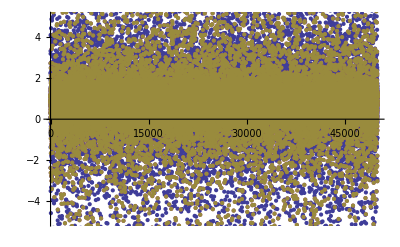

```mathematica
ListPlot[Transpose[(truePositions-convPositions)/truePositions],PlotRange->{-5,5}]
```

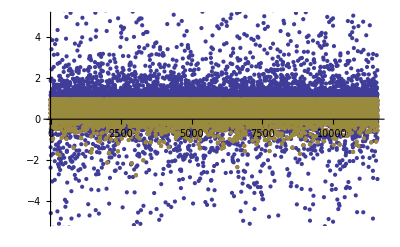

```mathematica
ListPlot[Transpose[(tpSel-cpSel)/tpSel],PlotRange->{-5,5}]
```

```mathematica
convDists=Sqrt[(convPositions[[All,1]]-8)^2+convPositions[[All,2]]^2+convPositions[[All,3]]^2];
```

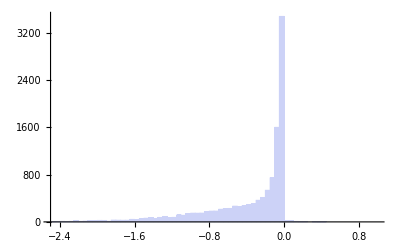

```mathematica
Histogram[Pick[Log10[Abs[(trueDists-convDists)]/trueDists],allSels],{-2.5,1,0.05}]
```

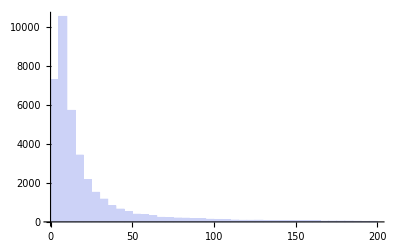

```mathematica
Histogram[Pick[convDists,Thread[!allSels]],{0,200,5}]
```

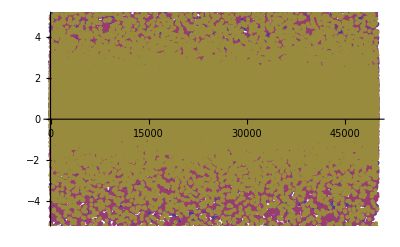

```mathematica
ListPlot[Transpose[(trueVelocities-convVelocities)/trueVelocities],PlotRange->{-5,5}]
```

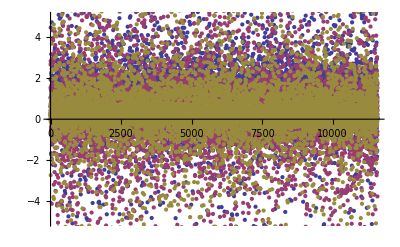

```mathematica
ListPlot[Transpose[(tvSel-cvSel)/tvSel],PlotRange->{-5,5}]
```

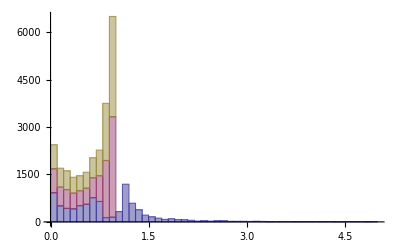

```mathematica
Histogram[Transpose[(tpSel-cpSel)/tpSel],{0,5,.1},ChartLayout->"Stacked"]
```

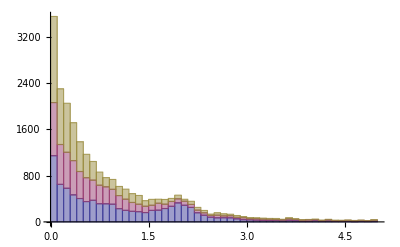

```mathematica
Histogram[Transpose[(tvSel-cvSel)/tvSel],{0,5,.1},ChartLayout->"Stacked"]
```

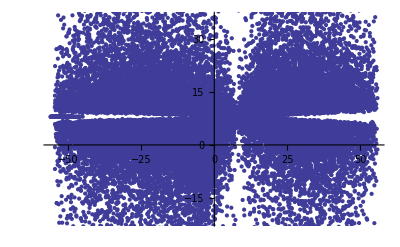

```mathematica
ListPlot[Transpose[{truePositions[[All,1]],convPositions[[All,1]]}]]
```

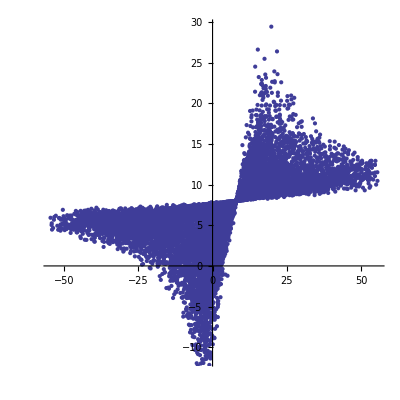

```mathematica
ListPlot[Transpose[{tpSel[[All,1]],cpSel[[All,1]]}],AspectRatio->1]
```

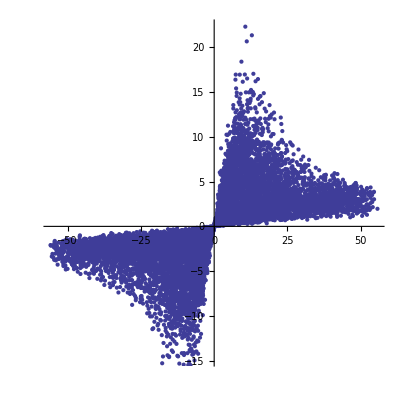

```mathematica
ListPlot[Transpose[{tpSel[[All,2]],cpSel[[All,2]]}],AspectRatio->1]
```

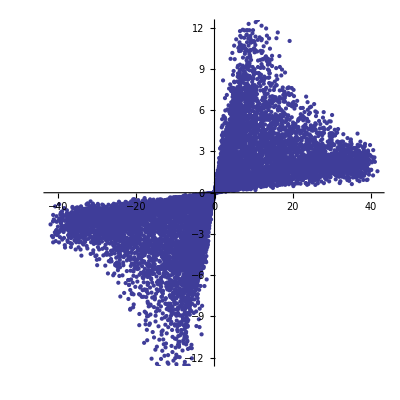

```mathematica
ListPlot[Transpose[{tpSel[[All,3]],cpSel[[All,3]]}],AspectRatio->1]
```

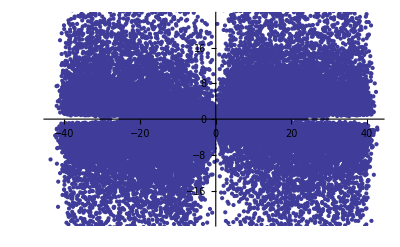

```mathematica
ListPlot[Transpose[{truePositions[[All,3]],convPositions[[All,3]]}]]
```

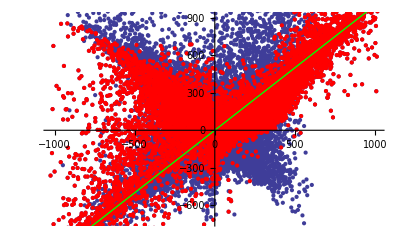

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,1]],convVelocities[[All,1]]}]],ListPlot[Transpose[{tvSel[[All,1]],cvSel[[All,1]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

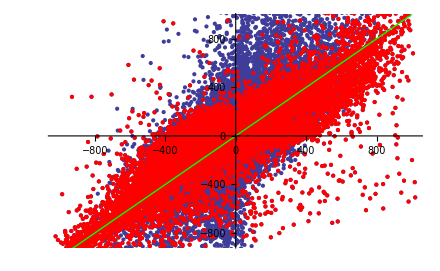

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,2]],convVelocities[[All,2]]}]],ListPlot[Transpose[{tvSel[[All,2]],cvSel[[All,2]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

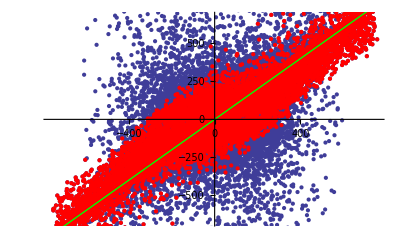

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,3]],convVelocities[[All,3]]}]],ListPlot[Transpose[{tvSel[[All,3]],cvSel[[All,3]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

Convert (x’,v’) to (Jr’,L’,Lz’)

```mathematica
fnameCleanPosIn="pos.clean.dat"
fnameCleanVelIn="vel.clean.dat"
```

pos.clean.dat

vel.clean.dat

```mathematica
pStream=OpenWrite[fnameCleanPosIn,BinaryFormat->False]
vStream=OpenWrite[fnameCleanVelIn,BinaryFormat->False]
```

OutputStream[pos.clean.dat,224]

OutputStream[vel.clean.dat,225]

```mathematica
Write[pStream,Length[cpSel]];
Export[pStream,cpSel,"Data"];
Export[vStream,cvSel,"Data"];
```

```mathematica
Close[pStream]
Close[vStream]
```

pos.clean.dat

vel.clean.dat

## At this point manually run cartToAA

```mathematica
Dimensions[convJ=ReadList["newJ.test.dat",{Number,Number,Number}]]
```

{1959,3}

Some stuff has unbound orbits, so select those out

```mathematica
Tally[boundSel=Thread[convJ[[All,3]]!=0]]
```

{{True,1848},{False,111}}

```mathematica
Dimensions[convJbound=Pick[convJ,boundSel]]
```

{1848,3}

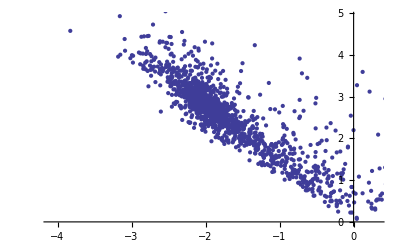

```mathematica
ListPlot[convJbound[[All,{1,2}]]]
```

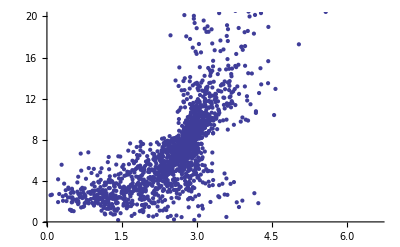

```mathematica
ListPlot[convJbound[[All,{2,3}]],PlotRange->{0,20}]
```

```mathematica
ListPointPlot3D[convJbound]
```

-Graphics3D-

```mathematica
Dimensions[tJSel=Pick[Pick[trueActions,allSels],boundSel]]
```

{1848,3}

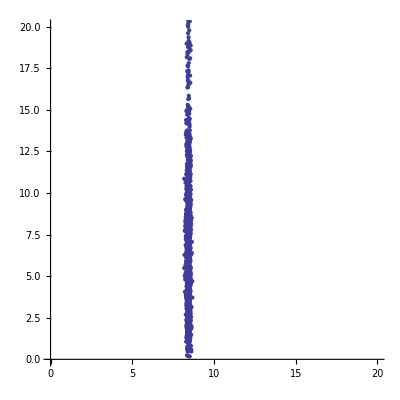

```mathematica
ListPlot[Transpose[{tJSel[[All,3]],convJbound[[All,3]]}],PlotRange->{{0,20},{0,20}},AspectRatio->1]
```

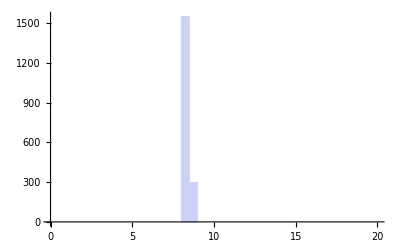

```mathematica
Histogram[tJSel[[All,3]],{0,20,.5}]
```

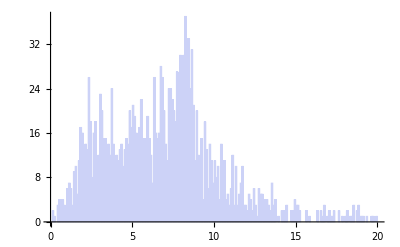

```mathematica
Histogram[convJbound[[All,3]],{0,20,.1}]
```

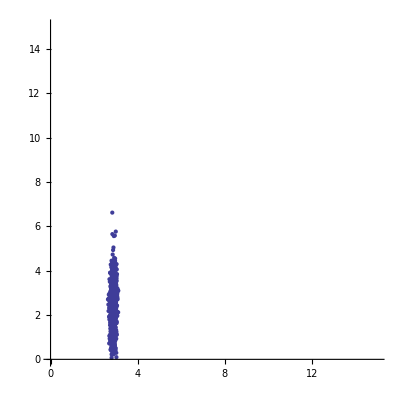

```mathematica
ListPlot[Transpose[{tJSel[[All,2]],convJbound[[All,2]]}],PlotRange->{{0,15},{0,15}},AspectRatio->1]
```

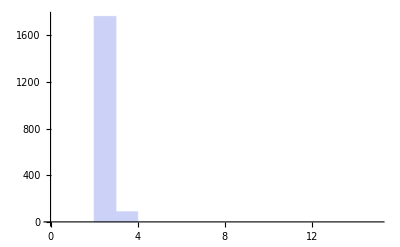

```mathematica
Histogram[tJSel[[All,2]],{0,15,1}]
```

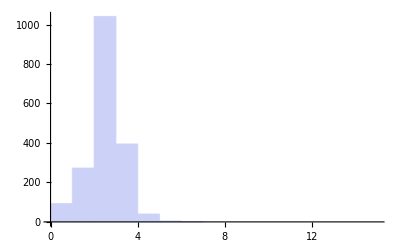

```mathematica
Histogram[convJbound[[All,2]],{0,15,1}]
```

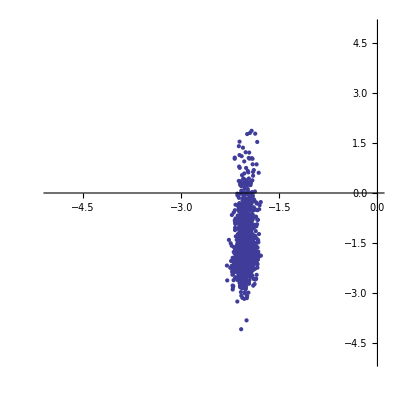

```mathematica
ListPlot[Transpose[{tJSel[[All,1]],convJbound[[All,1]]}],PlotRange->{{-5,0},{-5,5}},AspectRatio->1]
```

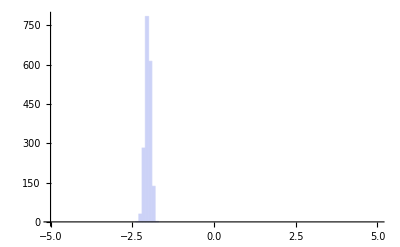

```mathematica
Histogram[tJSel[[All,1]],{-5,5,.1}]
```

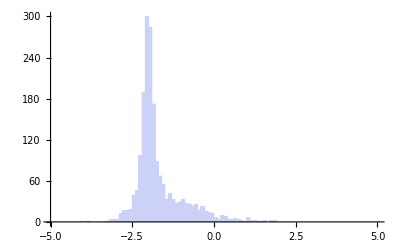

```mathematica
Histogram[convJbound[[All,1]],{-5,5,.1}]
```

Check by converting (x,v) unconvolved back to (Jr, L, Lz)

```mathematica
fnameCleanPosIn="posi.clean.dat"
fnameCleanVelIn="veli.clean.dat"
```

posi.clean.dat

veli.clean.dat

```mathematica
pStream=OpenWrite[fnameCleanPosIn,BinaryFormat->False]
vStream=OpenWrite[fnameCleanVelIn,BinaryFormat->False]
```

OutputStream[posi.clean.dat,201]

OutputStream[veli.clean.dat,202]

```mathematica
Write[pStream,Length[tpSel]];
Export[pStream,tpSel,"Data"];
Export[vStream,tvSel,"Data"];
```

```mathematica
Close[pStream]
Close[vStream]
```

posi.clean.dat

veli.clean.dat

## Run cartToAA

```mathematica
Dimensions[convJi=ReadList["newJi.test.dat",{Number,Number,Number}]]
```

{11584,3}

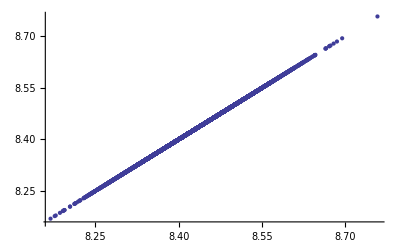

```mathematica
ListPlot[Transpose[{Pick[trueActions[[All,3]],allSels],convJi[[All,3]]}]]
```

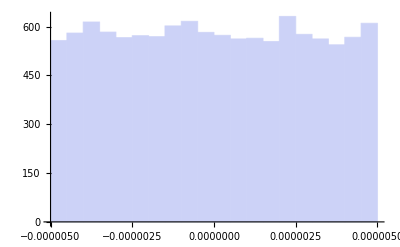

```mathematica
Histogram[Pick[trueActions[[All,3]],allSels]-convJi[[All,3]]]
```

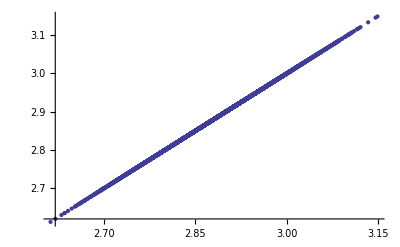

```mathematica
ListPlot[Transpose[{Pick[trueActions[[All,2]],allSels],convJi[[All,2]]}]]
```

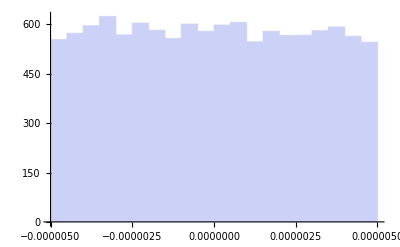

```mathematica
Histogram[Pick[trueActions[[All,2]],allSels]-convJi[[All,2]]]
```

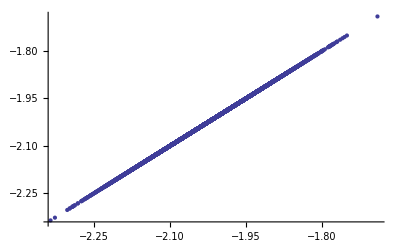

```mathematica
ListPlot[Transpose[{Pick[trueActions[[All,1]],allSels],convJi[[All,1]]}]]
```

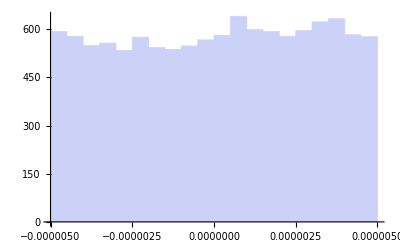

```mathematica
Histogram[Pick[trueActions[[All,1]],allSels]-convJi[[All,1]]]
```